```mathematica
(*y = Sqrt[m ω/hbar ] x *)

psi0[y_] = E^( -y^2/2)
psi1[y_] = y E^(-y^2/2) /2
psi2[y_] = (4 y^2 - 2) E^(-y^2/2) /8
```

ⅇ^(-y^2/2)

1/2 ⅇ^(-y^2/2) y

1/8 ⅇ^(-y^2/2) (-2+4 y^2)

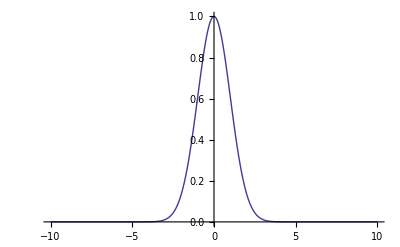

```mathematica
Plot[{psi0[y](*, Abs[psi0[y]]*)}, {y, -10, 10}, PlotRange ->Full]
```

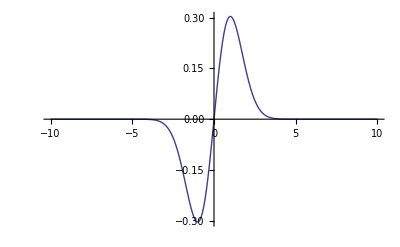

```mathematica
Plot[{psi1[y](*, Abs[psi1[y]]*)}, {y, -10, 10}, PlotRange ->Full]
```

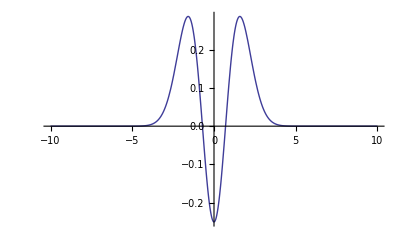

```mathematica
Plot[{psi2[y](*, Abs[psi2[y]]*)}, {y, -10, 10}, PlotRange ->Full]
```

```mathematica
SetDirectory["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit"]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit